## Probability of single and double resistance for the EG model with time-dependent rates

```mathematica
If[loopcount>1,Clear@@DeleteCases[Names@"`*","loopcount"|"file"]];
If[Head[loopcount]==Symbol, loopcount=1;]
```

### Input

```mathematica
minp=0.0;dp=0.1 ;maxp = 1.0;

dT =.05;maxT=1.5;
```

#### Constant rates

```mathematica
(*bS[t_]:=1.0;
bA[t_]:=1.1;
bB[t_]:=1.2;
bD[t_]:=1.3;
dS[t_]:=0.1;
dA[t_]:=minp+ dp*(loopcount-1) ;
dB[t_]:=0.1;
dD[t_]:=0.1 ;
μA= 1 10^-4;
μB= 1 10^-4;
n0 = 10000;
tmax=100;*)
```

#### Sinusoidal rates

```mathematica
(*P=1;ΔtA =0; ΔtB= minp +  dp*(loopcount-1);
CA[t_]:=Piecewise[{{0,t≤ΔtA},{ 1.0(Cos[(2Pi (t+P/2-ΔtA))/P]+1),t>ΔtA}}]; 
CB[t_]:=Piecewise[{{0,t≤ΔtB},{1.0(Cos[(2Pi (t+P/2-ΔtB))/P]+1),t>ΔtB}}];
fA[t_]:=1+CA[t];fB[t_]:=1+CB[t];
dS[t_]:=0.1fA[t]fB[t];
dA[t_]:=0.1fB[t]; 
dB[t_]:=0.1fA[t];
dD[t_]:=0.1; 
bS[t_]:=1.1/(fA[t]fB[t]); 
bA[t_]:=1.1/fB[t]; 
bB[t_]:=1.1/fA[t];
bD[t_]:=1.1; 
μA= 1 10^-3;
μB= 1 10^-3;
n0 = 5 10^3;
tmax=100;*)
```

#### Pulsing rates

```mathematica
(*P=1;I0 = 0; I1 = 2.0;ΔtA=0.0; ΔtB =minp +  dp*(loopcount-1);
CA0[t_]:=(I1-I0)/P^2(t-ΔtA-P)^2+I0; CA[t_]:=Piecewise[{{0,t≤ΔtA},{ CA0[Mod[t-ΔtA,P]+ΔtA],t>ΔtA}}]; 
CB0[t_]:=(I1-I0)/P^2(t-ΔtB-P)^2+I0; CB[t_]:=Piecewise[{{0,t≤ΔtB},{ CB0[Mod[t-ΔtB,P]+ΔtB],t>ΔtB}}]; 
αA=1/3; αB = 1/3;
bS[t_]:=1.0 - 2  αA αB(CA[t] + CB[t]); 
bA[t_]:=1.0 - αB CB[t]; 
bB[t_]:=1.0 -αA CA[t];
bD[t_]:=1;
μA= 1 10^-3;
μB= 1 10^-4;
dS[t_]:=0.1;
dA[t_]:=0.1; 
dB[t_]:=0.1;
dD[t_]:=0.1; 
n0 = 10^4;
tmax=100;*)
```

### Mean values

```mathematica
nsol=NDSolve[{nSe'[t]==(bS[t](1-μA-μB)-dS[t])nSe[t],nAe'[t]==(bA[t](1-μB)-dA[t])nAe[t]+bS[t]μA nSe[t],nBe'[t]==(bB[t](1-μA)-dB[t])nBe[t]+bS[t]μB nSe[t],nDe'[t]==(bD[t]-dD[t])nDe[t]+bA[t]μB nAe[t] + bB[t]μA nBe[t],nSe[0]==n0,nAe[0]==0,nBe[0]==0,nDe[0]==0} ,{nSe,nAe,nBe,nDe},{t,0,tmax},Method->{"DiscontinuityProcessing"->True}];
{nS, nA,nB,nD}=nsol[[1,All,2]];
```

### Single resistance

#### P_ext

```mathematica
nsolext=NDSolve[{nSex'[t]==(bS[t](1-μA-μB)-dS[t])nSex[t],nAex'[t]==(bA[t](1-μB)-dA[t])nAex[t],nBex'[t]==(bB[t](1-μA)-dB[t])nBex[t],nSex[0]==1,nAex[0]==1,nBex[0]==1} ,{nSex,nAex,nBex},{t,0,tmax}];
{nS0, nA0,nB0}=nsolext[[1,All,2]];
```

```mathematica
nAp[t_ ?NumericQ,tp_ ?NumericQ]:=nA0[tp]/nA0[t];nBp[t_ ?NumericQ,tp_ ?NumericQ]:=nB0[tp]/nB0[t];
```

```mathematica
PeFA[t_?NumericQ,T_?NumericQ] := NIntegrate[dA[tp]/nAp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
PeFB[t_?NumericQ,T_?NumericQ] := NIntegrate[dB[tp]/nBp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

```mathematica
PextA[t_,T_]:=PeFA[t,T]/(1 + PeFA[t,T]);PextB[t_,T_]:=PeFB[t,T]/(1 + PeFB[t,T]);
```

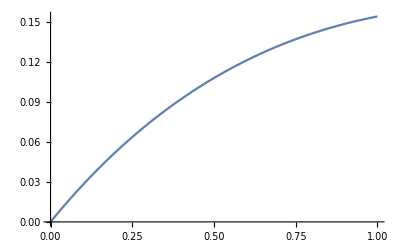

```mathematica
Plot[PextA[0,T],{T,0,1}]
```

#### Probability of single resistance

```mathematica
WA[t_]:=nS[t]bS[t]μA;
WB[t_]:=nS[t]bS[t]μB;
```

```mathematica
PRSingle[T_]:=1-Exp[NIntegrate[WA[t](PextA[t,T] - 1) + WB[t](PextB[t,T] - 1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

#### Save data

```mathematica
SetDirectory[NotebookDirectory[]];
filename = "param11-pulses-linear-PRS";
If[loopcount==1, Print["Total number of iterations: ",  (maxp-minp)/dp+1];DeleteFile[StringJoin[filename,".txt"]];file=OpenAppend[StringJoin[filename,".txt"]];]
Quiet[dataTable=Table[PRSingle[T],{T,0,maxT, dT}];]
Do[WriteString[file,StringJoin[ToString[dataTable[[i]], InputForm]],"\t"],{i,1,Length[dataTable]}];
WriteString[file,"\n"];
If[Mod[loopcount,1]==0,Print["iteration: ", loopcount]];
loopcount+=1; 
If[loopcount==(maxp-minp)/dp+2,Export[FileNameJoin[{Directory[],StringJoin[filename,"-time",".txt"]}],Table[T,{T,0,maxT, dT}],"Table","FieldSeparators"->" "];
Export[FileNameJoin[{Directory[],StringJoin[filename,"-parameter",".txt"]}],Table[p,{p,minp,maxp, dp}],"Table","FieldSeparators"->" "];Close[file];]
If[ loopcount <= (maxp-minp)/dp+1,NotebookEvaluate@EvaluationNotebook[]];
```

Total number of iterations: 11.

DeleteFile::fdnfnd: Directory or file param11-pulses-linear-PRS.txt not found.

iteration: 1

iteration: 2

iteration: 3

iteration: 4

iteration: 5

iteration: 6

iteration: 7

iteration: 8

iteration: 9

iteration: 10

iteration: 11

### Double resistance

#### P_ext

```mathematica
(*nsolext=NDSolve[{nDex'[t]==(bD[t]-dD[t])nDex[t],nDex[0]==1} ,{nDex},{t,0,tmax}];
{nD0}=nsolext[[1,All,2]];*)
```

```mathematica
(*nDp[t_ ?NumericQ,tp_ ?NumericQ]:=nD0[tp]/nD0[t];*)
```

```mathematica
(*PeFD[t_?NumericQ,T_?NumericQ] := NIntegrate[dD[tp]/nDp[t,tp],{tp,t,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];*)
```

```mathematica
(*PextD[t_,T_]:=PeFD[t,T]/(1 + PeFD[t,T]);*)
```

#### Probability of double resistance

```mathematica
(*WD[t_]:=nA[t]bA[t]μB + nB[t]bB[t]μA;*)
```

```mathematica
(*PRDouble[T_]:=1-Exp[NIntegrate[WD[t]*(PextD[t,T] - 1),{t,0,T},Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];*)
```

#### Save data

```mathematica
(*SetDirectory[NotebookDirectory[]];
filename = "param11-pulses-linear-PRD";
If[loopcount==1, Print["Total number of iterations: ",  (maxp-minp)/dp+1];DeleteFile[StringJoin[filename,".txt"]];file=OpenAppend[StringJoin[filename,".txt"]];]
Quiet[dataTable=Table[PRDouble[T],{T,0,maxT, dT}];]
Do[WriteString[file,StringJoin[ToString[dataTable[[i]], InputForm]],"\t"],{i,1,Length[dataTable]}];
WriteString[file,"\n"];
If[Mod[loopcount,1]==0,Print["iteration: ", loopcount]];
loopcount+=1; 
If[loopcount==(maxp-minp)/dp+2,Export[FileNameJoin[{Directory[],StringJoin[filename,"-time",".txt"]}],Table[T,{T,0,maxT, dT}],"Table","FieldSeparators"->" "];
Export[FileNameJoin[{Directory[],StringJoin[filename,"-parameter",".txt"]}],Table[p,{p,minp,maxp, dp}],"Table","FieldSeparators"->" "];Close[file];]
If[ loopcount <= (maxp-minp)/dp+1,NotebookEvaluate@EvaluationNotebook[]];*)
```